# 3 of 10 responsive subtypes

```mathematica
MeanNonResponseVolumeChange=20;
StandardDeviationOfVolumeChange=30;
GroupOfResponses[samplesize_,treatmenteffect_]:=RandomVariate[NormalDistribution[MeanNonResponseVolumeChange+treatmenteffect,StandardDeviationOfVolumeChange],samplesize]
```

```mathematica
ManyNonResponders=GroupOfResponses[200,0];
```

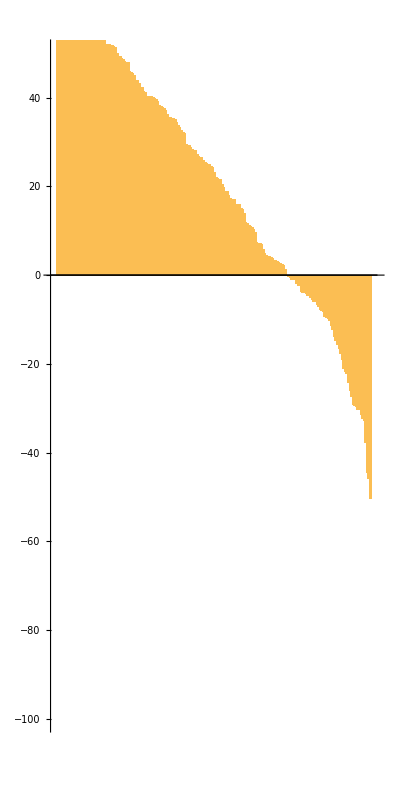

```mathematica
BarChart[Reverse[Sort[ManyNonResponders]],PlotRange->{-100,50},AspectRatio->2,ImageSize->{{250},{250}}]
```

```mathematica
(* treatment effect of '0' corresponds to 5% rate of Objective Response *)
ManyNonResponders=GroupOfResponses[100000,0];
Length[Select[ManyNonResponders,#<-30&]]/Length[ManyNonResponders]//N
```

0.04698

```mathematica
(* 30% rate of Objective Response (volume change below -30%) with treatment effect of -34 *)
ManyResponders=GroupOfResponses[100000,-34];
Length[Select[ManyResponders,#<-30&]]/Length[ManyResponders]//N
ManyResponders=GroupOfResponses[200,-34];
```

0.29611

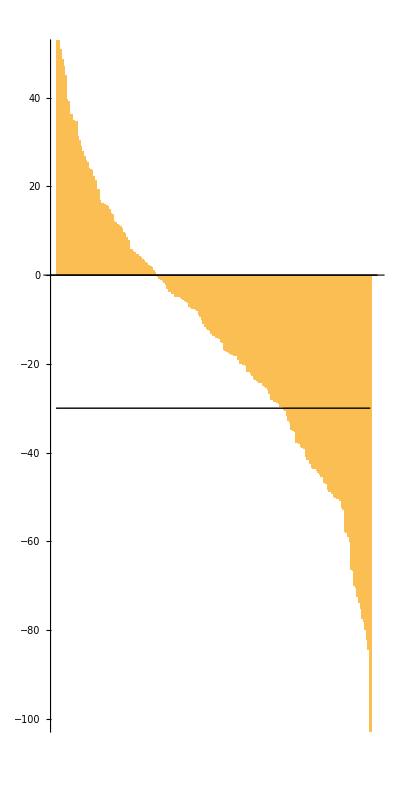

```mathematica
BarChart[Reverse[Sort[ManyResponders]],PlotRange->{-100,50},AspectRatio->2,Epilog->{Black,Line[{{0,-30},{200,-30}}]}]
```

```mathematica
(* Simon Two Stage Design population sizes with 80% Power, 10% type 1 error rate (one-sided), response rate for bad drug p0 = 10%, response rate for good drug p1 = 30%*)
Nstage1=7;
Nstage2=18;

(* number of responses required *)
ResponsesStage1=1;
ResponsesStage2=4;
```

```mathematica
TotalNumberOfTumorSubtypes=10;
NumberOfResponsiveSubtypes=2;
NumberOfExtraResponsiveSubtypes=1;
ExtraTreatmentEffect=2;(*the 'extra' responsive group has TWICE the treatment effect of others*)

NumberOfNonResponsiveSubtypes=TotalNumberOfTumorSubtypes-NumberOfResponsiveSubtypes-NumberOfExtraResponsiveSubtypes;
```

## Simon stage 1 assessment

```mathematica
Stage1ResponsesInGroups[treatmenteffect_]:=Join[
(* responding groups *)Table[GroupOfResponses[Nstage1,treatmenteffect],{NumberOfResponsiveSubtypes}],
(* extra-responsive group *)Table[GroupOfResponses[Nstage1,ExtraTreatmentEffect*treatmenteffect],{NumberOfExtraResponsiveSubtypes}],
(* non-responding groups *)Table[GroupOfResponses[Nstage1,0],{NumberOfNonResponsiveSubtypes}]
]
```

```mathematica
VolumeThresholdForResponse=-30;

SimonStage1Assessment[listofvolumes_]:=If[
Length[Select[listofvolumes,#<=VolumeThresholdForResponse&]]≥ResponsesStage1,
1,
0
]
```

```mathematica
Map[SimonStage1Assessment,Stage1ResponsesInGroups[-40]]
```

{0,1,1,0,0,0,0,0,0,0}

```mathematica
ManySimonStage1Assessments[numberofsimulations_,treatmenteffect_]:=Table[Map[SimonStage1Assessment,Stage1ResponsesInGroups[treatmenteffect]],{numberofsimulations}]
```

```mathematica
SimonStage1Power[numberofsimulations_,treatmenteffect_]:=Module[{},
SimulatedTrialAssessments=ManySimonStage1Assessments[numberofsimulations,treatmenteffect];

TrialsThatShouldBePositive=SimulatedTrialAssessments⟦All,1;;NumberOfResponsiveSubtypes⟧;
TrialsThatShouldBeNegative=SimulatedTrialAssessments⟦All,NumberOfResponsiveSubtypes+NumberOfExtraResponsiveSubtypes+1;;⟧;

PowerToDetectPositive=Total[Flatten[TrialsThatShouldBePositive]]/(NumberOfResponsiveSubtypes*numberofsimulations);

Type1ErrorRate=Total[Flatten[TrialsThatShouldBeNegative]]/(NumberOfNonResponsiveSubtypes*numberofsimulations);

{PowerToDetectPositive,Type1ErrorRate}
]
```

```mathematica
SimonStage1Power[1000,-40]//N
```

{0.958,0.294286}

```mathematica
SimonStage1PowerAndErrorRateVSEffect=Table[Flatten[{treatmenteffect,SimonStage1Power[1000,treatmenteffect]}],{treatmenteffect,-60,0,1}];
```

```mathematica
Export[NotebookDirectory[]<>"Simon test, stage 1.csv",SimonStage1PowerAndErrorRateVSEffect//N,"CSV"]
```

D:\Dropbox\Palmer, 2016\Basket trials submission\Revision\revision code\Simulations\False Positive Rate and Power\3 of 10 tumor types - and 1 is better\Simon test, stage 1.csv

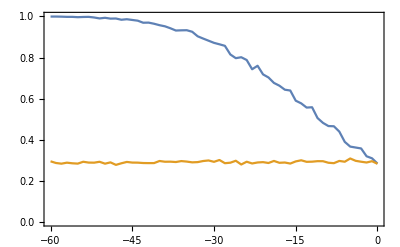

```mathematica
ListPlot[
{
SimonStage1PowerAndErrorRateVSEffect⟦All,{1,2}⟧
,
SimonStage1PowerAndErrorRateVSEffect⟦All,{1,3}⟧
},Joined->True,Frame->True,PlotRangePadding->None,PlotRange->{0,1}]
```

```mathematica
Mean[SimonStage1PowerAndErrorRateVSEffect⟦All,{1,3}⟧⟦All,2⟧]//N
```

0.290731

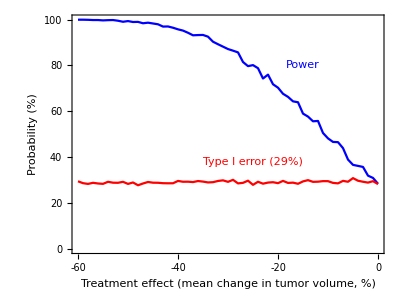

D:\Dropbox\Palmer, 2016\Basket trials submission\Revision\revision code\Simulations\False Positive Rate and Power\3 of 10 tumor types - and 1 is better\Simon stage 1 power and error.pdf

```mathematica
ListPlot[
{
SimonStage1PowerAndErrorRateVSEffect⟦All,{1,2}⟧
,
SimonStage1PowerAndErrorRateVSEffect⟦All,{1,3}⟧
},Joined->True,Frame->True,PlotRangePadding->False,PlotRange->{{-60,0},{0,1}},Axes->False,FrameStyle->Directive[Black,Thickness[Medium]],FrameTicks->{{Table[{i,100*i,{0.02,0}},{i,0,1,1/5}],Table[{i,,{0.02,0}},{i,0,1,1/5}]},{Table[{i,i,{0.02,0}},{i,-60,0,10}],Table[{i,,{0.02,0}},{i,-60,0,10}]}},FrameLabel->{"Treatment effect\n(mean change in tumor volume, %)","Probability (%)"},BaseStyle->{FontFamily->"Arial",FontSize->9},ImagePadding->{{40,10},{60,10}},AspectRatio->3/4,ImageSize->{{500},{170}},Epilog->{Blue,Text["Power",{-15,0.8},{0,0}],Red,Text["Type I error (29%)",{-25,0.38},{0,0}]}]/.{RGBColor[0.880722,0.611041,0.142051]->Red,RGBColor[0.368417,0.506779,0.709798]->Blue}

Export[NotebookDirectory[]<>"Simon stage 1 power and error.pdf",%,"PDF"]
```

## Simon stage 1 data, evaluated by Permutation testing

```mathematica
(* an initial function and parameter *)
NumberOfPermutations=10^5;
SignificanceOfMean[nulldistribution_,samplemean_]:=Length[Select[nulldistribution,#≤samplemean&]]/NumberOfPermutations
```

```mathematica
OneSimulatedTrialPermutationTestPower[treatmenteffect_]:=Module[{},
(* simulating a data set *)
SetOfResponses=Stage1ResponsesInGroups[treatmenteffect];

AllResponses=Flatten[SetOfResponses];
AverageResponsePerType=Map[Mean,SetOfResponses];
NullDistributionOfSampleMeans=Table[Mean[RandomSample[AllResponses,Nstage1]],{NumberOfPermutations}];
PValueBySubtype={
Join[Table[True,{NumberOfResponsiveSubtypes}],Table["ignore",{NumberOfExtraResponsiveSubtypes}],Table[False,{NumberOfNonResponsiveSubtypes}]],N[Map[SignificanceOfMean[NullDistributionOfSampleMeans,#]&,AverageResponsePerType]]
}ᵀ;
SortedPValues=Sort[PValueBySubtype,#1⟦2⟧<#2⟦2⟧&];
BHTable=Table[{
(* whether this is a group with a true effect or not *)SortedPValues⟦i,1⟧,
(* empiric P-value from null distribution *)SortedPValues⟦i,2⟧,
(* B-H critical value *)i/Length[SortedPValues]*(* Q = 0.25 *)0.25//N,
(* whether the P-value is within the BH critical value *)If[SortedPValues⟦i,2⟧<=i/Length[SortedPValues]*0.25,1,0]},{i,1,Length[SortedPValues]}];
AboveBHThresholdList=Reverse[Map[Min[{1,#}]&,Accumulate[Reverse[BHTable]⟦All,-1⟧]]];
BHTable={BHTable⟦All,1⟧,BHTable⟦All,2⟧,BHTable⟦All,3⟧,AboveBHThresholdList}ᵀ;

FractionOfTrueResponsesCorrectlyIdentified=Total[Select[BHTable,#⟦1⟧==True&]⟦All,-1⟧]/NumberOfResponsiveSubtypes;

FractionOfNonRespondersIncorrectlyIdentified=Total[Select[BHTable,#⟦1⟧==False&]⟦All,-1⟧]/NumberOfNonResponsiveSubtypes;

{FractionOfTrueResponsesCorrectlyIdentified,FractionOfNonRespondersIncorrectlyIdentified}
]
```

```mathematica
OneSimulatedTrialPermutationTestPower[-20]
```

{0,0}

```mathematica
ManySimulatedTrialsPermutationTestPower[numberofsimulations_,treatmenteffect_]:=Mean[Table[OneSimulatedTrialPermutationTestPower[treatmenteffect],{numberofsimulations}]]
```

```mathematica
ManySimulatedTrialsPermutationTestPower[10,-15]
```

{3/20,1/35}

```mathematica
PermutationStage1PowerAndErrorRateVSEffect=Parallelize[Table[Flatten[{treatmenteffect,ManySimulatedTrialsPermutationTestPower[200,treatmenteffect]}],{treatmenteffect,-60,0,2}]];
```

```mathematica
Export[NotebookDirectory[]<>"Permutation test, stage 1.csv",PermutationStage1PowerAndErrorRateVSEffect//N,"CSV"]
```

D:\Dropbox\Palmer, 2016\Basket trials submission\Revision\revision code\Simulations\False Positive Rate and Power\3 of 10 tumor types - and 1 is better\Permutation test, stage 1.csv

```mathematica
PermutationStage1PowerAndErrorRateVSEffect=Import[NotebookDirectory[]<>"Permutation test, stage 1.csv","CSV"];
```

```mathematica
SimonStage1PowerAndErrorRateVSEffect⟦All,{1,2}⟧//N
SimonStage1PowerAndErrorRateVSEffect⟦All,{1,3}⟧//N
```

{{-60.,0.9995},{-59.,0.9995},{-58.,0.999},{-57.,0.998},{-56.,0.998},{-55.,0.9965},{-54.,0.9975},{-53.,0.998},{-52.,0.995},{-51.,0.9905},{-50.,0.9935},{-49.,0.9895},{-48.,0.99},{-47.,0.984},{-46.,0.9865},{-45.,0.983},{-44.,0.9795},{-43.,0.9695},{-42.,0.97},{-41.,0.9645},{-40.,0.9575},{-39.,0.952},{-38.,0.9425},{-37.,0.9315},{-36.,0.9325},{-35.,0.933},{-34.,0.9255},{-33.,0.9035},{-32.,0.8925},{-31.,0.882},{-30.,0.8715},{-29.,0.8645},{-28.,0.857},{-27.,0.815},{-26.,0.797},{-25.,0.8015},{-24.,0.788},{-23.,0.743},{-22.,0.76},{-21.,0.718},{-20.,0.703},{-19.,0.6765},{-18.,0.663},{-17.,0.6435},{-16.,0.6395},{-15.,0.59},{-14.,0.577},{-13.,0.5565},{-12.,0.558},{-11.,0.5055},{-10.,0.482},{-9.,0.4665},{-8.,0.4655},{-7.,0.4395},{-6.,0.3895},{-5.,0.3665},{-4.,0.362},{-3.,0.3575},{-2.,0.3195},{-1.,0.3095},{0.,0.284}}

{{-60.,0.294857},{-59.,0.286714},{-58.,0.283429},{-57.,0.288286},{-56.,0.285286},{-55.,0.283714},{-54.,0.292714},{-53.,0.288714},{-52.,0.288286},{-51.,0.292571},{-50.,0.283429},{-49.,0.289714},{-48.,0.277571},{-47.,0.285286},{-46.,0.291857},{-45.,0.288714},{-44.,0.288429},{-43.,0.286571},{-42.,0.286143},{-41.,0.286286},{-40.,0.296429},{-39.,0.292857},{-38.,0.293143},{-37.,0.291429},{-36.,0.296},{-35.,0.293571},{-34.,0.289857},{-33.,0.291},{-32.,0.296286},{-31.,0.299},{-30.,0.292429},{-29.,0.301286},{-28.,0.285714},{-27.,0.288143},{-26.,0.297571},{-25.,0.279429},{-24.,0.292857},{-23.,0.284429},{-22.,0.289286},{-21.,0.290857},{-20.,0.286714},{-19.,0.296714},{-18.,0.287714},{-17.,0.289},{-16.,0.284},{-15.,0.294429},{-14.,0.299857},{-13.,0.292429},{-12.,0.293143},{-11.,0.295571},{-10.,0.295429},{-9.,0.287857},{-8.,0.285857},{-7.,0.296714},{-6.,0.292857},{-5.,0.308714},{-4.,0.297286},{-3.,0.292857},{-2.,0.289143},{-1.,0.295429},{0.,0.282714}}

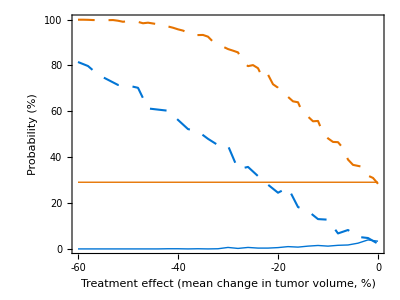

D:\Dropbox\Palmer, 2016\Basket trials submission\Revision\revision code\Simulations\False Positive Rate and Power\3 of 10 tumor types - and 1 is better\Stage 1, 7 patients, permutation vs simon.pdf

D:\Dropbox\Palmer, 2016\Basket trials submission\Revision\revision code\Simulations\False Positive Rate and Power\3 of 10 tumor types - and 1 is better\Stage 1, 7 patients, permutation vs simon.png

```mathematica
ListPlot[
{
PermutationStage1PowerAndErrorRateVSEffect⟦All,{1,2}⟧
,
PermutationStage1PowerAndErrorRateVSEffect⟦All,{1,3}⟧
,
SimonStage1PowerAndErrorRateVSEffect⟦All,{1,2}⟧
,
{{-60,Mean[SimonStage1PowerAndErrorRateVSEffect⟦All,3⟧]},{0,Mean[SimonStage1PowerAndErrorRateVSEffect⟦All,3⟧]}}
},
Joined->True,Frame->{{True,False},{True,False}},PlotRangePadding->{{0,0},{0.04,0.04}},PlotRange->{{-60,0},{0,1}},Axes->False,FrameStyle->Directive[Black,Thickness[Medium]],FrameTicks->{{Table[{i,100*i,{0,0.02}},{i,0,1,1/5}],Table[{i,,{0,0.02}},{i,0,1,1/5}]},{Join[Table[{i,i,{0,0.02}},{i,-60,0,20}],Table[{i,,{0,0.02}},{i,-50,-10,20}]],Table[{i,,{0,0.02}},{i,-60,0,10}]}},FrameLabel->{"Treatment effect   \n(mean change in tumor volume, %)    ","Probability (%)"},BaseStyle->{FontFamily->"Arial",FontSize->9},ImagePadding->{{40,10},{60,10}},AspectRatio->3/4,ImageSize->{{500},{170}},PlotStyle->{Directive[Darker[ColorData[3,6],0.1],Dashing[{0.03,0.025}],AbsoluteThickness[1.5],CapForm[None]],Directive[Darker[ColorData[3,6],0.1],AbsoluteThickness[1]],Directive[Darker[Orange,0.1],Dashing[{0.03,0.025}],CapForm[None],AbsoluteThickness[1.5]],Directive[Darker[Orange,0.1],AbsoluteThickness[1]]}]

Export[NotebookDirectory[]<>"Stage 1, 7 patients, permutation vs simon.pdf",%,"PDF"]
Export[NotebookDirectory[]<>"Stage 1, 7 patients, permutation vs simon.png",%%,"PNG",ImageResolution->600]
```

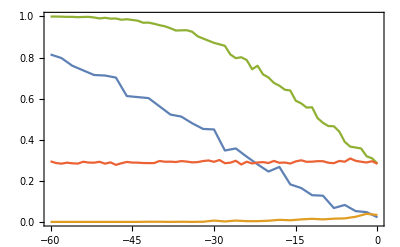

```mathematica
ListPlot[
{
PermutationStage1PowerAndErrorRateVSEffect⟦All,{1,2}⟧
,
PermutationStage1PowerAndErrorRateVSEffect⟦All,{1,3}⟧
,
SimonStage1PowerAndErrorRateVSEffect⟦All,{1,2}⟧
,
SimonStage1PowerAndErrorRateVSEffect⟦All,{1,3}⟧
},Joined->True,Frame->True,PlotRangePadding->None,PlotRange->{0,1}]
```

## Simon stage 2 assessment

```mathematica
Stage2ResponsesInGroups[treatmenteffect_]:=Join[
(* responding groups *)Table[GroupOfResponses[Nstage2,treatmenteffect],{NumberOfResponsiveSubtypes}],
(* extra-responsive group *)Table[GroupOfResponses[Nstage2,ExtraTreatmentEffect*treatmenteffect],{NumberOfExtraResponsiveSubtypes}],
(* non-responding groups *)Table[GroupOfResponses[Nstage2,0],{NumberOfNonResponsiveSubtypes}]
]
```

```mathematica
VolumeThresholdForResponse=-30;

SimonStage2Assessment[listofvolumes_]:=If[
Length[Select[listofvolumes,#<=VolumeThresholdForResponse&]]≥ResponsesStage2,
1,
0
]
```

```mathematica
Map[SimonStage2Assessment,Stage2ResponsesInGroups[-40]]
```

{1,1,1,0,0,0,0,0,0,0}

```mathematica
ManySimonStage2Assessments[numberofsimulations_,treatmenteffect_]:=Table[Map[SimonStage2Assessment,Stage2ResponsesInGroups[treatmenteffect]],{numberofsimulations}]
```

```mathematica
SimonStage2Power[numberofsimulations_,treatmenteffect_]:=Module[{},
SimulatedTrialAssessments=ManySimonStage2Assessments[numberofsimulations,treatmenteffect];

TrialsThatShouldBePositive=SimulatedTrialAssessments⟦All,1;;NumberOfResponsiveSubtypes⟧;
TrialsThatShouldBeNegative=SimulatedTrialAssessments⟦All,NumberOfResponsiveSubtypes+NumberOfExtraResponsiveSubtypes+1;;⟧;

PowerToDetectPositive=Total[Flatten[TrialsThatShouldBePositive]]/(NumberOfResponsiveSubtypes*numberofsimulations);

Type1ErrorRate=Total[Flatten[TrialsThatShouldBeNegative]]/(NumberOfNonResponsiveSubtypes*numberofsimulations);

{PowerToDetectPositive,Type1ErrorRate}
]
```

```mathematica
SimonStage2Power[1000,-40]//N
```

{0.946,0.00871429}

```mathematica
SimonStage2PowerAndErrorRateVSEffect=Table[Flatten[{treatmenteffect,SimonStage2Power[1000,treatmenteffect]}],{treatmenteffect,-60,0,1}];
```

```mathematica
Export[NotebookDirectory[]<>"Simon test, stage 2.csv",SimonStage2PowerAndErrorRateVSEffect//N,"CSV"]
```

D:\Dropbox\Palmer, 2016\Basket trials submission\Revision\revision code\Simulations\False Positive Rate and Power\3 of 10 tumor types - and 1 is better\Simon test, stage 2.csv

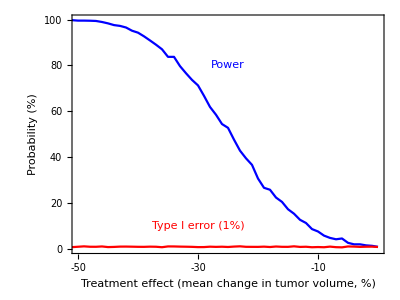

```mathematica
ListPlot[
{
SimonStage2PowerAndErrorRateVSEffect⟦All,{1,2}⟧
,
SimonStage2PowerAndErrorRateVSEffect⟦All,{1,3}⟧
},Joined->True,Frame->True,PlotRangePadding->False,PlotRange->{{-50,0},{0,1}},Axes->False,FrameStyle->Directive[Black,Thickness[Medium]],FrameTicks->{{Table[{i,100*i,{0.02,0}},{i,0,1,1/5}],Table[{i,,{0.02,0}},{i,0,1,1/5}]},{Table[{i,i,{0.02,0}},{i,-50,0,10}],Table[{i,,{0.02,0}},{i,-50,0,10}]}},FrameLabel->{"Treatment effect\n(mean change in tumor volume, %)","Probability (%)"},BaseStyle->{FontFamily->"Arial",FontSize->9},ImagePadding->{{40,10},{60,10}},AspectRatio->3/4,ImageSize->{{500},{170}},Epilog->{Blue,Text["Power",{-25,0.8},{0,0}],Red,Text["Type I error (1%)",{-30,0.1},{0,0}]}]/.{RGBColor[0.880722,0.611041,0.142051]->Red,RGBColor[0.368417,0.506779,0.709798]->Blue}
```

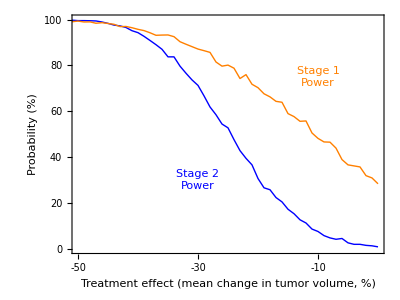

D:\Dropbox\Palmer, 2016\Basket trials submission\Revision\revision code\Simulations\False Positive Rate and Power\3 of 10 tumor types - and 1 is better\Simon stage 1 vs stage 2 power.pdf

```mathematica
ListPlot[
{
SimonStage2PowerAndErrorRateVSEffect⟦All,{1,2}⟧
,
SimonStage1PowerAndErrorRateVSEffect⟦All,{1,2}⟧
},Joined->True,Frame->True,PlotRangePadding->False,PlotRange->{{-50,0},{0,1}},Axes->False,FrameStyle->Directive[Black,Thickness[Medium]],FrameTicks->{{Table[{i,100*i,{0.02,0}},{i,0,1,1/5}],Table[{i,,{0.02,0}},{i,0,1,1/5}]},{Table[{i,i,{0.02,0}},{i,-50,0,10}],Table[{i,,{0.02,0}},{i,-50,0,10}]}},FrameLabel->{"Treatment effect\n(mean change in tumor volume, %)","Probability (%)"},BaseStyle->{FontFamily->"Arial",FontSize->9},ImagePadding->{{40,10},{60,10}},AspectRatio->3/4,ImageSize->{{500},{170}},Epilog->{Blue,Text["Stage 2\nPower",{-30,0.3},{0,0}],Orange,Text["Stage 1\nPower",{-10,0.75},{0,0}]},PlotStyle->{Directive[Blue,AbsoluteThickness[1]],Directive[Orange,AbsoluteThickness[1]]}]

Export[NotebookDirectory[]<>"Simon stage 1 vs stage 2 power.pdf",%,"PDF"]
```

## Simon stage 2 data, evaluated by Permutation testing

```mathematica
(* an initial function and parameter *)
NumberOfPermutations=10^5;
SignificanceOfMean[nulldistribution_,samplemean_]:=Length[Select[nulldistribution,#≤samplemean&]]/NumberOfPermutations
```

```mathematica
OneSimulatedTrialPermutationTestPower[treatmenteffect_]:=Module[{},
(* simulating a data set *)
SetOfResponses=Stage2ResponsesInGroups[treatmenteffect];

AllResponses=Flatten[SetOfResponses];
AverageResponsePerType=Map[Mean,SetOfResponses];
NullDistributionOfSampleMeans=Table[Mean[RandomSample[AllResponses,Nstage2]],{NumberOfPermutations}];
PValueBySubtype={
Join[Table[True,{NumberOfResponsiveSubtypes}],Table["Ignore",{NumberOfExtraResponsiveSubtypes}],Table[False,{NumberOfNonResponsiveSubtypes}]],N[Map[SignificanceOfMean[NullDistributionOfSampleMeans,#]&,AverageResponsePerType]]
}ᵀ;
SortedPValues=Sort[PValueBySubtype,#1⟦2⟧<#2⟦2⟧&];
BHTable=Table[{
(* whether this is a group with a true effect or not *)SortedPValues⟦i,1⟧,
(* empiric P-value from null distribution *)SortedPValues⟦i,2⟧,
(* B-H critical value *)i/Length[SortedPValues]*(* Q = 0.25 *)0.25//N,
(* whether the P-value is within the BH critical value *)If[SortedPValues⟦i,2⟧<=i/Length[SortedPValues]*0.25,1,0]},{i,1,Length[SortedPValues]}];
AboveBHThresholdList=Reverse[Map[Min[{1,#}]&,Accumulate[Reverse[BHTable]⟦All,-1⟧]]];
BHTable={BHTable⟦All,1⟧,BHTable⟦All,2⟧,BHTable⟦All,3⟧,AboveBHThresholdList}ᵀ;

FractionOfTrueResponsesCorrectlyIdentified=Total[Select[BHTable,#⟦1⟧==True&]⟦All,-1⟧]/NumberOfResponsiveSubtypes;

FractionOfNonRespondersIncorrectlyIdentified=Total[Select[BHTable,#⟦1⟧==False&]⟦All,-1⟧]/NumberOfNonResponsiveSubtypes;

{FractionOfTrueResponsesCorrectlyIdentified,FractionOfNonRespondersIncorrectlyIdentified}
]
```

```mathematica
OneSimulatedTrialPermutationTestPower[-20]
```

{1,0}

```mathematica
ManySimulatedTrialsPermutationTestPower[numberofsimulations_,treatmenteffect_]:=Mean[Table[OneSimulatedTrialPermutationTestPower[treatmenteffect],{numberofsimulations}]]
```

```mathematica
ManySimulatedTrialsPermutationTestPower[10,-20]
```

{11/20,0}

```mathematica
PermutationStage2PowerAndErrorRateVSEffect=Parallelize[Table[Flatten[{treatmenteffect,ManySimulatedTrialsPermutationTestPower[1000,treatmenteffect]}],{treatmenteffect,-60,0,2}]];
```

```mathematica
Export[NotebookDirectory[]<>"Permutation test, stage 2.csv",PermutationStage2PowerAndErrorRateVSEffect//N,"CSV"]
```

D:\Dropbox\Palmer, 2016\Basket trials submission\Revision\revision code\Simulations\False Positive Rate and Power\3 of 10 tumor types - and 1 is better\Permutation test, stage 2.csv

```mathematica
PermutationStage2PowerAndErrorRateVSEffect=Import[NotebookDirectory[]<>"Permutation test, stage 2.csv","CSV"];
```

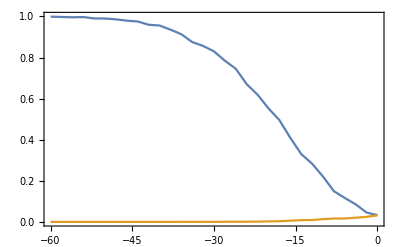

```mathematica
ListPlot[
{
PermutationStage2PowerAndErrorRateVSEffect⟦All,{1,2}⟧
,
PermutationStage2PowerAndErrorRateVSEffect⟦All,{1,3}⟧
},Joined->True,Frame->True,PlotRangePadding->None,PlotRange->{0,1}]
```

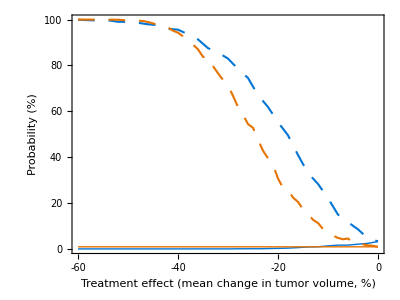

D:\Dropbox\Palmer, 2016\Basket trials submission\Revision\revision code\Simulations\False Positive Rate and Power\3 of 10 tumor types - and 1 is better\Stage 2, 25 patients, permutation vs simon.pdf

D:\Dropbox\Palmer, 2016\Basket trials submission\Revision\revision code\Simulations\False Positive Rate and Power\3 of 10 tumor types - and 1 is better\Stage 2, 25 patients, permutation vs simon.png

```mathematica
ListPlot[
{
PermutationStage2PowerAndErrorRateVSEffect⟦All,{1,2}⟧
,
PermutationStage2PowerAndErrorRateVSEffect⟦All,{1,3}⟧
,
SimonStage2PowerAndErrorRateVSEffect⟦All,{1,2}⟧
,
{{-60,Mean[SimonStage2PowerAndErrorRateVSEffect⟦All,3⟧]},{0,Mean[SimonStage2PowerAndErrorRateVSEffect⟦All,3⟧]}}
},
Joined->True,Frame->{{True,False},{True,False}},PlotRangePadding->{{0,0},{0.04,0.04}},PlotRange->{{-60,0},{0,1}},Axes->False,FrameStyle->Directive[Black,Thickness[Medium]],FrameTicks->{{Table[{i,100*i,{0,0.02}},{i,0,1,1/5}],Table[{i,,{0,0.02}},{i,0,1,1/5}]},{Join[Table[{i,i,{0,0.02}},{i,-60,0,20}],Table[{i,,{0,0.02}},{i,-50,-10,20}]],Table[{i,,{0,0.02}},{i,-60,0,10}]}},FrameLabel->{"Treatment effect   \n(mean change in tumor volume, %)    ","Probability (%)"},BaseStyle->{FontFamily->"Arial",FontSize->9},ImagePadding->{{40,10},{60,10}},AspectRatio->3/4,ImageSize->{{500},{170}},PlotStyle->{Directive[Darker[ColorData[3,6],0.1],Dashing[{0.03,0.025}],AbsoluteThickness[1.5],CapForm[None]],Directive[Darker[ColorData[3,6],0.1],AbsoluteThickness[1]],Directive[Darker[Orange,0.1],Dashing[{0.03,0.025}],CapForm[None],AbsoluteThickness[1.5]],Directive[Darker[Orange,0.1],AbsoluteThickness[1]]}]

Export[NotebookDirectory[]<>"Stage 2, 25 patients, permutation vs simon.pdf",%,"PDF"]
Export[NotebookDirectory[]<>"Stage 2, 25 patients, permutation vs simon.png",%%,"PNG",ImageResolution->600]
```

#### comparison of type 2 error rates (false negative)

```mathematica
SimonType1ErrorAtMinus30Shrinkage=Select[SimonStage2PowerAndErrorRateVSEffect⟦All,{1,3}⟧,#⟦1⟧==-30&]⟦1,2⟧//N
PermutationType1ErrorAtMinus30Shrinkage=Select[PermutationStage2PowerAndErrorRateVSEffect⟦All,{1,3}⟧,#⟦1⟧==-30&]⟦1,2⟧//N

(*ratio*)
SimonType1ErrorAtMinus30Shrinkage/PermutationType1ErrorAtMinus30Shrinkage

SimonType2ErrorAtMinus30Shrinkage=1-Select[SimonStage2PowerAndErrorRateVSEffect⟦All,{1,2}⟧,#⟦1⟧==-30&]⟦1,2⟧//N
PermutationType2ErrorAtMinus30Shrinkage=1-Select[PermutationStage2PowerAndErrorRateVSEffect⟦All,{1,2}⟧,#⟦1⟧==-30&]⟦1,2⟧//N

(*ratio*)
SimonType2ErrorAtMinus30Shrinkage/PermutationType2ErrorAtMinus30Shrinkage
```

0.00785714

0.

Power::infy: Infinite expression 1/0. encountered.

ComplexInfinity

0.287

0.17

1.68824

```mathematica
MyMovingMedian[list_]:=Join[
{list⟦1⟧,Median[list⟦{1,2,3}⟧]},
MovingMedian[list,5],
{Median[list⟦{-1,-2,-3}⟧],list⟦-1⟧}
]
```

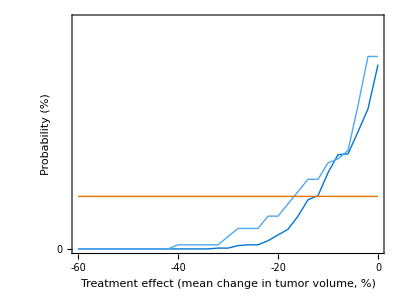

```mathematica
ListPlot[
{
MyMovingMedian[PermutationStage2PowerAndErrorRateVSEffect⟦All,{1,3}⟧]
,
MyMovingMedian[PermutationStage1PowerAndErrorRateVSEffect⟦All,{1,3}⟧]
,
{{-60,Mean[SimonStage2PowerAndErrorRateVSEffect⟦All,3⟧]},{0,Mean[SimonStage2PowerAndErrorRateVSEffect⟦All,3⟧]}}
},
Joined->True,Frame->{{True,False},{True,False}},PlotRangePadding->{{0,0},{0.003,0.003}},PlotRange->{{-60,0},{0,0.04}},Axes->False,FrameStyle->Directive[Black,Thickness[Medium]],FrameTicks->{{Table[{i,100*i,{0,0.02}},{i,0,1,1/100}],Table[{i,,{0,0.02}},{i,0,1,1/100}]},{Join[Table[{i,i,{0,0.02}},{i,-60,0,20}],Table[{i,,{0,0.02}},{i,-50,-10,20}]],Table[{i,,{0,0.02}},{i,-60,0,10}]}},FrameLabel->{"Treatment effect   \n(mean change in tumor volume, %)    ","Probability (%)"},BaseStyle->{FontFamily->"Arial",FontSize->9},ImagePadding->{{40,10},{60,10}},AspectRatio->3/4,ImageSize->{{500},{160}},PlotStyle->{Directive[Darker[ColorData[3,6],0.1],AbsoluteThickness[1]],Directive[Lighter[ColorData[3,6],0.3],AbsoluteThickness[1]],Directive[Darker[Orange,0.1],AbsoluteThickness[1]]}]
```

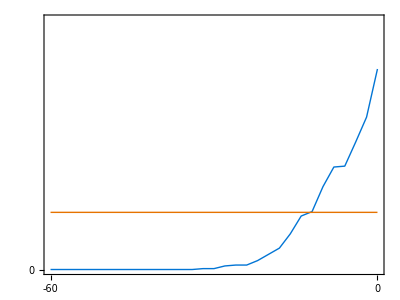

D:\Dropbox\Palmer, 2016\Basket trials submission\Revision\revision code\Simulations\False Positive Rate and Power\3 of 10 tumor types - and 1 is better\Stage 2, 25 patients, type 1 error inset.pdf

D:\Dropbox\Palmer, 2016\Basket trials submission\Revision\revision code\Simulations\False Positive Rate and Power\3 of 10 tumor types - and 1 is better\Stage 2, 25 patients, type 1 error inset.png

```mathematica
ListPlot[
{
MyMovingMedian[PermutationStage2PowerAndErrorRateVSEffect⟦All,{1,3}⟧]
,
{{-60,Mean[SimonStage2PowerAndErrorRateVSEffect⟦All,3⟧]},{0,Mean[SimonStage2PowerAndErrorRateVSEffect⟦All,3⟧]}}
},
Joined->True,Frame->{{True,False},{True,False}},PlotRangePadding->{{0,0},{0.003,0.003}},PlotRange->{{-60,0},{0,0.04}},Axes->False,FrameStyle->Directive[Black,Thickness[Medium]],FrameTicks->{{Table[{i,100*i,{0,0.05}},{i,0,1,1/50}],Table[{i,,{0,0.03}},{i,0,1,1/60}]},{Join[Table[{i,i,{0,0.05}},{i,-60,0,60}],Table[{i,,{0,0.03}},{i,-50,-10,10}]],Table[{i,,{0,0.03}},{i,-60,0,10}]}},BaseStyle->{FontFamily->"Arial",FontSize->8},ImagePadding->{{40,10},{60,10}},AspectRatio->3/4,ImageSize->{{500},{100}},PlotStyle->{Directive[Darker[ColorData[3,6],0.1],AbsoluteThickness[1]],Directive[Darker[Orange,0.1],AbsoluteThickness[1]]}]


Export[NotebookDirectory[]<>"Stage 2, 25 patients, type 1 error inset.pdf",%,"PDF"]
Export[NotebookDirectory[]<>"Stage 2, 25 patients, type 1 error inset.png",%%,"PNG",ImageResolution->600]
```

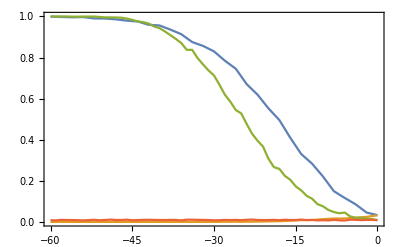

```mathematica
ListPlot[
{
PermutationStage2PowerAndErrorRateVSEffect⟦All,{1,2}⟧
,
PermutationStage2PowerAndErrorRateVSEffect⟦All,{1,3}⟧
,
SimonStage2PowerAndErrorRateVSEffect⟦All,{1,2}⟧
,
SimonStage2PowerAndErrorRateVSEffect⟦All,{1,3}⟧
},Joined->True,Frame->True,PlotRangePadding->None,PlotRange->{0,1}]
```

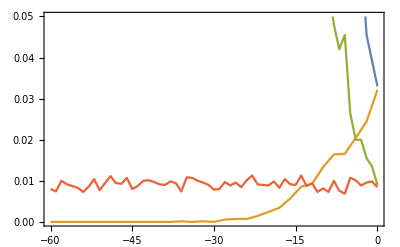

```mathematica
ListPlot[
{
PermutationStage2PowerAndErrorRateVSEffect⟦All,{1,2}⟧
,
PermutationStage2PowerAndErrorRateVSEffect⟦All,{1,3}⟧
,
SimonStage2PowerAndErrorRateVSEffect⟦All,{1,2}⟧
,
SimonStage2PowerAndErrorRateVSEffect⟦All,{1,3}⟧
},Joined->True,Frame->True,PlotRangePadding->None,PlotRange->{0,0.05}]
```

```mathematica
MyMovingMedian[list_]:=Join[
{list⟦1⟧,Median[list⟦{1,2,3}⟧]},
MovingMedian[list,5],
{Median[list⟦{-1,-2,-3}⟧],list⟦-1⟧}
]
```

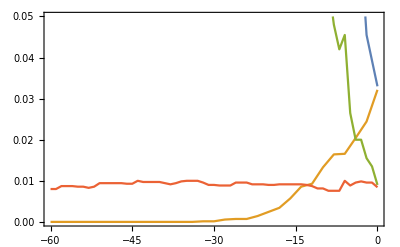

```mathematica
ListPlot[
{
PermutationStage2PowerAndErrorRateVSEffect⟦All,{1,2}⟧
,
MyMovingMedian[PermutationStage2PowerAndErrorRateVSEffect⟦All,{1,3}⟧]
,
SimonStage2PowerAndErrorRateVSEffect⟦All,{1,2}⟧
,
MyMovingMedian[SimonStage2PowerAndErrorRateVSEffect⟦All,{1,3}⟧]
},Joined->True,Frame->True,PlotRangePadding->None,PlotRange->{0,0.05}]
```